## Offset Curves

```mathematica
func={u,u^2/2}
```

{u,u^2/2}

```mathematica
d=0.5;
```

```mathematica
funX=u;
funY=u^2/2;
dx=D[funX,u];
dy=D[funY,u];
```

```mathematica
offsetX=funX-(d dy)/(√(dx^2+dy^2));
offsetY=funY+(d dx)/(√(dx^2+dy^2));
```

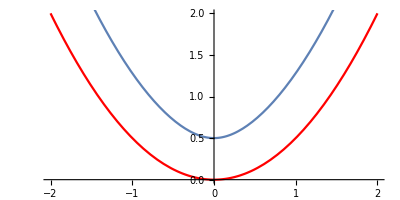

```mathematica
Show[{ParametricPlot[func,{u,-2,2},PlotStyle->Red],ParametricPlot[{offsetX,offsetY},{u,-2,2}]}]
```